# Hybrid Modes

Generated by tools/make_PNModes_nb.wls from PNpedia commit a64de8b. Rerun the script rather than editing the definitions by hand.

```mathematica
Clear["Global`*"]
```

## Conventions

Waveform decomposition (PNpedia README of the Waveform folders): h = h+ - i hx = (G m/(c^2 R)) Sum_lm h_lm e^(-i m psi) Y^(-2)_lm(theta, phi), with psi the tail-shifted phase (Honet eq. 9). Only m > 0 modes are listed; h_(l,-m) = (-1)^l Conjugate[h_lm]. G = c = 1, m = M total mass.

Variables: x = (M omega_22/2)^(2/3) frequency parameter of the (2,2) mode; ν = m1 m2/M^2; δ = (m1 - m2)/M = Sqrt[1 - 4 ν]; s = (m1^2 χ1 + m2^2 χ2)/M^2; σ = (m2 χ2 - m1 χ1)/M.

Spin map for a spinning primary (m1, the heavier body, spin χ) and a nonspinning secondary (Honet eq. B6: a = m1 χ, S = m1 a, Σ = -M a).

```mathematica
δOf[ν_] := Sqrt[1 - 4*ν];
sOf[ν_, χ_] := ((1 + δOf[ν])/2)^2*χ;
σOf[ν_, χ_] := -((1 + δOf[ν])/2)*χ;
```

Each mode is written as (Newtonian prefactor c ν x^n0) * (sum over x^k terms). The prefactor is the leading nonspinning term with ν -> 0, δ -> 1; the ν-dependence of the leading term (Honet's α_lm) stays inside the bracket.

## PN Data

## Nonspinning

hNS[l, m][x, ν, δ]: nonspinning h_lm through 3.5PN (δ appears in odd-m modes).

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Nonspinning/Without tidal effects/Waveform/h_l_m.txt
   <- Henry, Faye, Blanchet 2022, arXiv:2210.15602v2, eqs. (3.2), (3.4). 3.5PN. *)

(* (2,1) *)
hNS[2, 1][x_, ν_, δ_] := ((8*I)/3)*Sqrt[Pi/5]*x^(3/2)*ν*(
    x^(0)*(δ) +
    x^(1)*((-17*δ)/28 + (5*δ*ν)/7) +
    x^(3/2)*(Pi*δ - (I/2)*δ*(1 + Log[16])) +
    x^(2)*((-43*δ)/126 - (509*δ*ν)/126 + (79*δ*ν^2)/168) +
    x^(5/2)*((-17*δ*(2*Pi - I*(1 + Log[16])))/56 + (δ*ν*(6*Pi - I*(353 + Log[4096])))/28) +
    x^(3)*(((-1633904 + 60885*Pi^2)*δ*ν)/38016 - (4211*δ*ν^2)/8316 + (2263*δ*ν^3)/8316 + δ*(15223771/1455300 - (214*EulerGamma)/105 + Pi^2/6 + Pi*((109*I)/210 - (2*I)*Log[2]) - (319*Log[2])/105 - 2*Log[2]^2) - (107*δ*Log[x])/105));

(* (2,2) *)
hNS[2, 2][x_, ν_, δ_] := 8*Sqrt[Pi/5]*x*ν*(
    x^(0)*(1) +
    x^(1)*(-107/42 + (55*ν)/42) +
    x^(3/2)*(2*Pi) +
    x^(2)*(-2173/1512 - (1069*ν)/216 + (2047*ν^2)/1512) +
    x^(5/2)*((-107*Pi)/21 + (-24*I + (34*Pi)/21)*ν) +
    x^(3)*(27027409/646800 - (856*EulerGamma)/105 + ((428*I)/105)*Pi + (2*Pi^2)/3 + (41*(-13570 + 693*Pi^2)*ν)/66528 - (20261*ν^2)/2772 + (114635*ν^3)/99792 - (1712*Log[2])/105 - (428*Log[x])/105) +
    x^(7/2)*((-2173*Pi)/756 + ((100331*I - 7485*Pi)*ν)/1134 + (2*(-2033*I + 700*Pi)*ν^2)/945));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Nonspinning/Without tidal effects/Waveform/h_l_m.txt
   <- Henry, Faye, Blanchet 2022, arXiv:2210.15602v2, eqs. (3.2), (3.4). 3.5PN. *)

(* (3,1) *)
hNS[3, 1][x_, ν_, δ_] := (I/3)*Sqrt[(2*Pi)/35]*x^(3/2)*ν*(
    x^(0)*(δ) +
    x^(1)*((-8*δ)/3 - (2*δ*ν)/3) +
    x^(3/2)*(δ*((-7*I)/5 + Pi - (2*I)*Log[2])) +
    x^(2)*((607*δ)/198 - (136*δ*ν)/99 - (247*δ*ν^2)/198) +
    x^(5/2)*(-1/30*(δ*ν*(2*I + 35*Pi - (70*I)*Log[2])) - (8*δ*(5*Pi - I*(7 + Log[1024])))/15) +
    x^(3)*((-1738843/154440 + (41*Pi^2)/64)*δ*ν + (327059*δ*ν^2)/30888 - (17525*δ*ν^3)/15444 + δ*(10753397/1513512 - (26*EulerGamma)/21 + Pi^2/6 - (424*Log[2])/105 - 2*Log[2]^2 - ((2*I)/105)*Pi*(41 + 105*Log[2])) - (13*δ*Log[x])/21));

(* (3,2) *)
hNS[3, 2][x_, ν_, δ_] := (8*Sqrt[Pi/7]*x^2*ν)/3*(
    x^(0)*(1 - 3*ν) +
    x^(1)*(-193/90 + (145*ν)/18 - (73*ν^2)/18) +
    x^(3/2)*(-3*I + 2*Pi + ((66*I)/5 - 6*Pi)*ν) +
    x^(2)*(-1451/3960 - (17387*ν)/3960 + (5557*ν^2)/220 - (5341*ν^3)/1320) +
    x^(5/2)*((-193*(-3*I + 2*Pi))/90 + ((-258929*I)/5400 + (136*Pi)/9)*ν + ((33751*I)/450 - (46*Pi)/9)*ν^2));

(* (3,3) *)
hNS[3, 3][x_, ν_, δ_] := (-3*I)*Sqrt[(6*Pi)/7]*x^(3/2)*ν*(
    x^(0)*(δ) +
    x^(1)*(-4*δ + 2*δ*ν) +
    x^(3/2)*(3*Pi*δ + ((3*I)/5)*δ*(-7 + Log[59049/1024])) +
    x^(2)*((123*δ)/110 - (1838*δ*ν)/165 + (887*δ*ν^2)/330) +
    x^(5/2)*(δ*ν*((-48103*I)/1215 + (9*Pi)/2 - (9*I)*Log[2] + (9*I)*Log[3]) + (12*δ*(-5*Pi + I*(7 - 10*Log[3] + Log[1024])))/5) +
    x^(3)*((-7055/3432 + (41*Pi^2)/64)*δ*ν - (318841*δ*ν^2)/17160 + (8237*δ*ν^3)/2860 + δ*(19388147/280280 - (78*EulerGamma)/7 + (3*Pi^2)/2 - (1272*Log[2])/35 - 18*Log[2]^2 - ((6*I)/35)*Pi*(41 + 105*Log[2] - 105*Log[3]) + (492*Log[3])/35 + 36*Log[2]*Log[3] - 18*Log[3]^2) - (39*δ*Log[x])/7));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Nonspinning/Without tidal effects/Waveform/h_l_m.txt
   <- Henry, Faye, Blanchet 2022, arXiv:2210.15602v2, eqs. (3.2), (3.4). 3.5PN. *)

(* (4,1) *)
hNS[4, 1][x_, ν_, δ_] := (I/105)*Sqrt[2*Pi]*x^(5/2)*ν*(
    x^(0)*(δ - 2*δ*ν) +
    x^(1)*((-101*δ)/33 + (337*δ*ν)/44 - (83*δ*ν^2)/33) +
    x^(3/2)*(δ*((-32*I)/15 + Pi - (2*I)*Log[2]) + δ*ν*((1661*I)/30 - 2*Pi + (4*I)*Log[2])) +
    x^(2)*((42982*δ)/15015 - (513989*δ*ν)/51480 + (196957*δ*ν^2)/10296 - (1195*δ*ν^3)/572));

(* (4,2) *)
hNS[4, 2][x_, ν_, δ_] := (8*Sqrt[Pi]*x^2*ν)/63*(
    x^(0)*(1 - 3*ν) +
    x^(1)*(-437/110 + (805*ν)/66 - (19*ν^2)/22) +
    x^(3/2)*((-21*I)/5 + 2*Pi + ((84*I)/5 - 6*Pi)*ν) +
    x^(2)*(1038039/200200 - (606751*ν)/28600 + (400453*ν^2)/25740 + (25783*ν^3)/17160) +
    x^(5/2)*((-437*(-21*I + 10*Pi))/550 + ((-83029*I)/880 + (772*Pi)/33)*ν + ((93081*I)/1100 + (14*Pi)/11)*ν^2));

(* (4,3) *)
hNS[4, 3][x_, ν_, δ_] := ((-9*I)/5)*Sqrt[(2*Pi)/7]*x^(5/2)*ν*(
    x^(0)*(δ - 2*δ*ν) +
    x^(1)*((-39*δ)/11 + (1267*δ*ν)/132 - (131*δ*ν^2)/33) +
    x^(3/2)*(δ*((-32*I)/5 + 3*Pi - (6*I)*Log[2] + (6*I)*Log[3]) + δ*ν*((16301*I)/810 - 6*Pi + (12*I)*Log[2] - (12*I)*Log[3])) +
    x^(2)*((7206*δ)/5005 - (82869*δ*ν)/5720 + (104839*δ*ν^2)/3432 - (2987*δ*ν^3)/572));

(* (4,4) *)
hNS[4, 4][x_, ν_, δ_] := (-64*Sqrt[Pi/7]*x^2*ν)/9*(
    x^(0)*(1 - 3*ν) +
    x^(1)*(-593/110 + (1273*ν)/66 - (175*ν^2)/22) +
    x^(3/2)*((-42*I)/5 + 4*Pi + ν*((1193*I)/40 - 12*Pi - (24*I)*Log[2]) + (8*I)*Log[2]) +
    x^(2)*(1068671/200200 - (1088119*ν)/28600 + (146879*ν^2)/2340 - (226097*ν^3)/17160) +
    x^(5/2)*((-593*(-21*I + 10*Pi + (20*I)*Log[2]))/275 + ν^2*((4096237*I)/21120 - (284*Pi)/11 - ((568*I)/11)*Log[2]) + ν*((-31525499*I)/140800 + (2480*Pi)/33 + ((4960*I)/33)*Log[2])));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Nonspinning/Without tidal effects/Waveform/h_l_m.txt
   <- Henry, Faye, Blanchet 2022, arXiv:2210.15602v2, eqs. (3.2), (3.4). 3.5PN. *)

(* (5,1) *)
hNS[5, 1][x_, ν_, δ_] := (I/180)*Sqrt[Pi/77]*x^(5/2)*ν*(
    x^(0)*(δ - 2*δ*ν) +
    x^(1)*((-179*δ)/39 + (352*δ*ν)/39 - (4*δ*ν^2)/39) +
    x^(3/2)*(δ*((-181*I)/70 + Pi - (2*I)*Log[2]) + δ*ν*((626*I)/5 - 2*Pi + (4*I)*Log[2])) +
    x^(2)*((5023*δ)/585 - (49447*δ*ν)/2340 + (68*δ*ν^2)/9 + (287*δ*ν^3)/117));

(* (5,2) *)
hNS[5, 2][x_, ν_, δ_] := (16*Sqrt[Pi/11]*x^3*ν)/135*(
    x^(0)*(1 - 5*ν + 5*ν^2) +
    x^(1)*(-3911/910 + (3079*ν)/130 - (413*ν^2)/13 + (231*ν^3)/26) +
    x^(3/2)*((-26*I)/5 + 2*Pi + ((16237*I)/336 - 10*Pi)*ν + ((-1861*I)/20 + 10*Pi)*ν^2));

(* (5,3) *)
hNS[5, 3][x_, ν_, δ_] := ((-9*I)/20)*Sqrt[(3*Pi)/22]*x^(5/2)*ν*(
    x^(0)*(δ - 2*δ*ν) +
    x^(1)*((-69*δ)/13 + (464*δ*ν)/39 - (88*δ*ν^2)/39) +
    x^(3/2)*(δ*((-543*I)/70 + 3*Pi - (6*I)*Log[2] + (6*I)*Log[3]) + δ*ν*((83702*I)/3645 - 6*Pi + (12*I)*Log[2] - (12*I)*Log[3])) +
    x^(2)*((12463*δ)/1365 - (56969*δ*ν)/1820 + (2172*δ*ν^2)/91 - (365*δ*ν^3)/273));

(* (5,4) *)
hNS[5, 4][x_, ν_, δ_] := (-256*Sqrt[Pi/33]*x^3*ν)/45*(
    x^(0)*(1 - 5*ν + 5*ν^2) +
    x^(1)*(-4451/910 + (3619*ν)/130 - (521*ν^2)/13 + (339*ν^3)/26) +
    x^(3/2)*((-52*I)/5 + 4*Pi + ν*((3351011*I)/53760 - 20*Pi - (40*I)*Log[2]) + ν^2*((-10923*I)/128 + 20*Pi + (40*I)*Log[2]) + (8*I)*Log[2]));

(* (5,5) *)
hNS[5, 5][x_, ν_, δ_] := ((125*I)/12)*Sqrt[(5*Pi)/66]*x^(5/2)*ν*(
    x^(0)*(δ - 2*δ*ν) +
    x^(1)*((-263*δ)/39 + (688*δ*ν)/39 - (256*δ*ν^2)/39) +
    x^(3/2)*(δ*((-181*I)/14 + 5*Pi - (10*I)*Log[2] + (10*I)*Log[5]) + δ*ν*((105834*I)/3125 - 10*Pi + (20*I)*Log[2] - (20*I)*Log[5])) +
    x^(2)*((9185*δ)/819 - (188765*δ*ν)/3276 + (54428*δ*ν^2)/819 - (10567*δ*ν^3)/819));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Nonspinning/Without tidal effects/Waveform/h_l_m.txt
   <- Henry, Faye, Blanchet 2022, arXiv:2210.15602v2, eqs. (3.2), (3.4). 3.5PN. *)

(* (6,1) *)
hNS[6, 1][x_, ν_, δ_] := (I/2079)*Sqrt[(2*Pi)/65]*x^(7/2)*ν*(
    x^(0)*(δ - 4*δ*ν + 3*δ*ν^2) +
    x^(1)*((-125*δ)/24 + (277*δ*ν)/12 - (289*δ*ν^2)/12 + (17*δ*ν^3)/3));

(* (6,2) *)
hNS[6, 2][x_, ν_, δ_] := (16*Sqrt[Pi/13]*x^3*ν)/1485*(
    x^(0)*(1 - 5*ν + 5*ν^2) +
    x^(1)*(-81/14 + (59*ν)/2 - 32*ν^2 + (7*ν^3)/2) +
    x^(3/2)*((-83*I)/14 + 2*Pi + ((799789*I)/13440 - 10*Pi)*ν + ((-19193*I)/160 + 10*Pi)*ν^2));

(* (6,3) *)
hNS[6, 3][x_, ν_, δ_] := ((-81*I)/385)*Sqrt[Pi/13]*x^(7/2)*ν*(
    x^(0)*(δ - 4*δ*ν + 3*δ*ν^2) +
    x^(1)*((-133*δ)/24 + (301*δ*ν)/12 - (329*δ*ν^2)/12 + 7*δ*ν^3));

(* (6,4) *)
hNS[6, 4][x_, ν_, δ_] := (-1024*Sqrt[(2*Pi)/195]*x^3*ν)/495*(
    x^(0)*(1 - 5*ν + 5*ν^2) +
    x^(1)*(-93/14 + (71*ν)/2 - 44*ν^2 + (19*ν^3)/2) +
    x^(3/2)*((-83*I)/7 + 4*Pi + ν*((3432215*I)/49152 - 20*Pi - (40*I)*Log[2]) + ν^2*((-382365*I)/4096 + 20*Pi + (40*I)*Log[2]) + (8*I)*Log[2]));

(* (6,5) *)
hNS[6, 5][x_, ν_, δ_] := ((625*I)/63)*Sqrt[(5*Pi)/429]*x^(7/2)*ν*(
    x^(0)*(δ - 4*δ*ν + 3*δ*ν^2) +
    x^(1)*((-149*δ)/24 + (349*δ*ν)/12 - (409*δ*ν^2)/12 + (29*δ*ν^3)/3));

(* (6,6) *)
hNS[6, 6][x_, ν_, δ_] := (432*Sqrt[Pi/715]*x^3*ν)/5*(
    x^(0)*(1 - 5*ν + 5*ν^2) +
    x^(1)*(-113/14 + (91*ν)/2 - 64*ν^2 + (39*ν^3)/2) +
    x^(3/2)*(6*Pi + ν*((21787499*I)/217728 - 30*Pi - (60*I)*Log[3]) + ν^2*((-323903*I)/2592 + 30*Pi + (60*I)*Log[3]) + ((3*I)/14)*(-83 + 56*Log[3])));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Nonspinning/Without tidal effects/Waveform/h_l_m.txt
   <- Henry, Faye, Blanchet 2022, arXiv:2210.15602v2, eqs. (3.2), (3.4). 3.5PN. *)

(* (7,1) *)
hNS[7, 1][x_, ν_, δ_] := (I/108108)*Sqrt[Pi/10]*x^(7/2)*ν*(
    x^(0)*(δ - 4*δ*ν + 3*δ*ν^2) +
    x^(1)*((-223*δ)/34 + (1361*δ*ν)/51 - (1118*δ*ν^2)/51 + (38*δ*ν^3)/17));

(* (7,2) *)
hNS[7, 2][x_, ν_, δ_] := (8*Sqrt[Pi/15]*x^4*ν)/3003*(
    x^(0)*(1 - 7*ν + 14*ν^2 - 7*ν^3));

(* (7,3) *)
hNS[7, 3][x_, ν_, δ_] := ((-243*I)/20020)*Sqrt[(3*Pi)/10]*x^(7/2)*ν*(
    x^(0)*(δ - 4*δ*ν + 3*δ*ν^2) +
    x^(1)*((-239*δ)/34 + (1505*δ*ν)/51 - (1358*δ*ν^2)/51 + (70*δ*ν^3)/17));

(* (7,4) *)
hNS[7, 4][x_, ν_, δ_] := (-1024*Sqrt[(2*Pi)/165]*x^4*ν)/1365*(
    x^(0)*(1 - 7*ν + 14*ν^2 - 7*ν^3));

(* (7,5) *)
hNS[7, 5][x_, ν_, δ_] := ((3125*I)/3276)*Sqrt[(5*Pi)/66]*x^(7/2)*ν*(
    x^(0)*(δ - 4*δ*ν + 3*δ*ν^2) +
    x^(1)*((-271*δ)/34 + (1793*δ*ν)/51 - (1838*δ*ν^2)/51 + (134*δ*ν^3)/17));

(* (7,6) *)
hNS[7, 6][x_, ν_, δ_] := (648*Sqrt[(3*Pi)/715]*x^4*ν)/35*(
    x^(0)*(1 - 7*ν + 14*ν^2 - 7*ν^3));

(* (7,7) *)
hNS[7, 7][x_, ν_, δ_] := ((-16807*I)/180)*Sqrt[(7*Pi)/4290]*x^(7/2)*ν*(
    x^(0)*(δ - 4*δ*ν + 3*δ*ν^2) +
    x^(1)*((-319*δ)/34 + (2225*δ*ν)/51 - (2558*δ*ν^2)/51 + (230*δ*ν^3)/17));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Nonspinning/Without tidal effects/Waveform/h_l_m.txt
   <- Henry, Faye, Blanchet 2022, arXiv:2210.15602v2, eqs. (3.2), (3.4). 3.5PN. *)

(* (8,1) *)
hNS[8, 1][x_, ν_, δ_] := (I/92664)*Sqrt[Pi/1190]*x^(9/2)*ν*(
    x^(0)*(δ - 6*δ*ν + 10*δ*ν^2 - 4*δ*ν^3));

(* (8,2) *)
hNS[8, 2][x_, ν_, δ_] := (8*Sqrt[Pi/17]*x^4*ν)/45045*(
    x^(0)*(1 - 7*ν + 14*ν^2 - 7*ν^3));

(* (8,3) *)
hNS[8, 3][x_, ν_, δ_] := ((-81*I)/3640)*Sqrt[(3*Pi)/374]*x^(9/2)*ν*(
    x^(0)*(δ - 6*δ*ν + 10*δ*ν^2 - 4*δ*ν^3));

(* (8,4) *)
hNS[8, 4][x_, ν_, δ_] := (-1024*Sqrt[(2*Pi)/935]*x^4*ν)/4095*(
    x^(0)*(1 - 7*ν + 14*ν^2 - 7*ν^3));

(* (8,5) *)
hNS[8, 5][x_, ν_, δ_] := ((15625*I)/4536)*Sqrt[(5*Pi)/4862]*x^(9/2)*ν*(
    x^(0)*(δ - 6*δ*ν + 10*δ*ν^2 - 4*δ*ν^3));

(* (8,6) *)
hNS[8, 6][x_, ν_, δ_] := (1944*Sqrt[(3*Pi)/85085]*x^4*ν)/35*(
    x^(0)*(1 - 7*ν + 14*ν^2 - 7*ν^3));

(* (8,7) *)
hNS[8, 7][x_, ν_, δ_] := ((-117649*I)/3240)*Sqrt[(7*Pi)/4862]*x^(9/2)*ν*(
    x^(0)*(δ - 6*δ*ν + 10*δ*ν^2 - 4*δ*ν^3));

(* (8,8) *)
hNS[8, 8][x_, ν_, δ_] := (-131072*Sqrt[(2*Pi)/17017]*x^4*ν)/315*(
    x^(0)*(1 - 7*ν + 14*ν^2 - 7*ν^3));
```

### 4PN term of h22

```mathematica
(* Source: PNpedia (commit a64de8b) Publications/arXiv-2304.11186v4/Equation (6.17).txt
   <- Blanchet, Faye, Henry, Larrouturou, Trestini 2023, arXiv:2304.11186v4, eq. (6.17) (also eq. (11) of arXiv:2304.11185v4).
   Only the 4PN (x^4) term of h22 / (8 Sqrt[Pi/5] ν x); lower orders are in hNS[2, 2]. *)
hNS4PN[2, 2][x_, ν_] := 8*Sqrt[Pi/5]*ν*x*(x^4*(-846557506853/12713500800 + (45796*EulerGamma)/2205 - ((22898*I)/2205)*Pi - (107*Pi^2)/63 + (256450291/7413120 - (1025*Pi^2)/1008)*ν^2 - (81579187*ν^3)/15567552 + (26251249*ν^4)/31135104 + (22898*Log[16*x])/2205 + ν*(-336005827477/4237833600 + (15284*EulerGamma)/441 - ((219314*I)/2205)*Pi - (9755*Pi^2)/32256 + (7642*Log[16*x])/441)));
```

```mathematica
(8*Sqrt[Pi/5]*ν*x)(hNS[2,2][x,ν,δ]/(8*Sqrt[Pi/5]*ν*x)+hNS4PN[2, 2][x, ν]/(8*Sqrt[Pi/5]*ν*x))
```

8 √(π/5) x ν (1+2 π x^(3/2)+x (-107/42+(55 ν)/42)+x^(5/2) (-(107 π)/21+(-24 ⅈ+(34 π)/21) ν)+x^2 (-2173/1512-(1069 ν)/216+(2047 ν^2)/1512)+x^(7/2) (-(2173 π)/756+((100331 ⅈ-7485 π) ν)/1134+2/945 (-2033 ⅈ+700 π) ν^2)+x^3 (27027409/646800-(856 EulerGamma)/105+(428 ⅈ π)/105+(2 π^2)/3+(41 (-13570+693 π^2) ν)/66528-(20261 ν^2)/2772+(114635 ν^3)/99792-(1712 Log[2])/105-(428 Log[x])/105)+x^4 (-846557506853/12713500800+(45796 EulerGamma)/2205-(22898 ⅈ π)/2205-(107 π^2)/63+(256450291/7413120-(1025 π^2)/1008) ν^2-(81579187 ν^3)/15567552+(26251249 ν^4)/31135104+(22898 Log[16 x])/2205+ν (-336005827477/4237833600+(15284 EulerGamma)/441-(219314 ⅈ π)/2205-(9755 π^2)/32256+7642/441 Log[16 x])))

## Spin-orbit

hSO[l, m][x, ν, δ, s, σ]: terms linear in the spins, through 3.5PN.

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 1 in the spins (s, σ) of the PNpedia expression. *)

(* (2,1) *)
hSO[2, 1][x_, ν_, δ_, s_, σ_] := ((8*I)/3)*Sqrt[Pi/5]*x^(3/2)*ν*(
    x^(1/2)*((3*σ)/2) +
    x^(3/2)*((-86*s*δ - 79*σ)/14 + (139*ν*σ)/14) +
    x^(2)*((3*σ*(2*Pi - I*(1 + Log[16])))/4) +
    x^(5/2)*((ν*(3088*s*δ - 2615*σ))/504 - (1723*ν^2*σ)/126 + (-331*s*δ + 293*σ)/252) +
    x^(3)*((s*δ*(181*I - 430*Pi + (860*I)*Log[2]))/70 + (ν*σ*(2570*Pi - I*(5853 + 5140*Log[2])))/280 + (79*σ*(-2*Pi + I*(1 + Log[16])))/28));

(* (2,2) *)
hSO[2, 2][x_, ν_, δ_, s_, σ_] := 8*Sqrt[Pi/5]*x*ν*(
    x^(3/2)*((-2*(3*s + δ*σ))/3) +
    x^(5/2)*((-4*ν*(23*s - 5*δ*σ))/63 + (-163*s - 3*δ*σ)/63) +
    x^(3)*((-4*((I + 3*Pi)*s + Pi*δ*σ))/3) +
    x^(7/2)*((ν^2*(1497*s + 1025*δ*σ))/252 + (13*ν*(2799*s + 1202*δ*σ))/756 + (9549*s + 3931*δ*σ)/756));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 1 in the spins (s, σ) of the PNpedia expression. *)

(* (3,1) *)
hSO[3, 1][x_, ν_, δ_, s_, σ_] := (I/3)*Sqrt[(2*Pi)/35]*x^(3/2)*ν*(
    x^(3/2)*((-15*ν*σ)/2 + (s*δ + 5*σ)/2) +
    x^(5/2)*((-79*s*δ - 149*σ)/18 - (841*ν^2*σ)/18 + (ν*(443*s*δ + 700*σ))/18) +
    x^(3)*((s*δ*(47*I + 10*Pi - (20*I)*Log[2]))/20 + (ν*σ*(11*I - 150*Pi + (300*I)*Log[2]))/20 + (σ*(5*Pi - I*(7 + Log[1024])))/2));

(* (3,2) *)
hSO[3, 2][x_, ν_, δ_, s_, σ_] := (8*Sqrt[Pi/7]*x^2*ν)/3*(
    x^(1/2)*(2*(s + δ*σ)) +
    x^(3/2)*(-13*s - (31*δ*σ)/3 + ν*((73*s)/3 + 10*δ*σ)) +
    x^(2)*((-2*I + 4*Pi)*s + 2*(-3*I + 2*Pi)*δ*σ) +
    x^(5/2)*(ν*((-15413*s)/396 - (1616*δ*σ)/55) + ν^2*((-419*s)/44 - (16153*δ*σ)/1980) + (14577*s + 19241*δ*σ)/1980));

(* (3,3) *)
hSO[3, 3][x_, ν_, δ_, s_, σ_] := (-3*I)*Sqrt[(6*Pi)/7]*x^(3/2)*ν*(
    x^(3/2)*((-7*s*δ - 3*σ)/2 + (9*ν*σ)/2) +
    x^(5/2)*(ν*((-83*s*δ)/30 - 12*σ) - (5*ν^2*σ)/2 + (139*s*δ + 129*σ)/30) +
    x^(3)*(ν*σ*((-8797*I)/540 + (27*Pi)/2 - (27*I)*Log[2] + (27*I)*Log[3]) - (3*(70*Pi*s*δ + 30*Pi*σ - I*s*δ*(71 + 140*Log[2] - 140*Log[3]) + (6*I)*σ*(-7 + Log[59049/1024])))/20));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 1 in the spins (s, σ) of the PNpedia expression. *)

(* (4,1) *)
hSO[4, 1][x_, ν_, δ_, s_, σ_] := (I/105)*Sqrt[2*Pi]*x^(5/2)*ν*(
    x^(1/2)*((-15*ν*σ)/2 + (5*(s*δ + σ))/2) +
    x^(3/2)*((-1147*s*δ - 927*σ)/66 - (555*ν^2*σ)/22 + (ν*(1139*s*δ + 3480*σ))/66) +
    x^(2)*((ν*σ*(181*I - 90*Pi + (180*I)*Log[2]))/12 + (30*Pi*s*δ + 30*Pi*σ - (4*I)*σ*(16 + 15*Log[2]) - I*s*δ*(53 + 60*Log[2]))/12));

(* (4,2) *)
hSO[4, 2][x_, ν_, δ_, s_, σ_] := (8*Sqrt[Pi]*x^2*ν)/63*(
    x^(3/2)*((-4*(s - 9*δ*σ))/15 + (4*ν*(s - 6*δ*σ))/5) +
    x^(5/2)*((-2*(129*s + 313*δ*σ))/55 - (3*ν^2*(1387*s + 725*δ*σ))/55 + (ν*(6653*s + 6698*δ*σ))/165));

(* (4,3) *)
hSO[4, 3][x_, ν_, δ_, s_, σ_] := ((-9*I)/5)*Sqrt[(2*Pi)/7]*x^(5/2)*ν*(
    x^(1/2)*((-15*ν*σ)/2 + (5*(s*δ + σ))/2) +
    x^(3/2)*((-1303*s*δ - 1083*σ)/66 - (815*ν^2*σ)/22 + (ν*(1451*s*δ + 4260*σ))/66) +
    x^(2)*((30*Pi*σ + s*δ*(30*Pi - I*(53 + 60*Log[2] - 60*Log[3])) - (4*I)*σ*(16 + 15*Log[2] - 15*Log[3]))/4 + ν*σ*((6007*I)/108 - (45*Pi)/2 + (45*I)*Log[2] - (45*I)*Log[3])));

(* (4,4) *)
hSO[4, 4][x_, ν_, δ_, s_, σ_] := (-64*Sqrt[Pi/7]*x^2*ν)/9*(
    x^(3/2)*((4*ν*(19*s + 6*δ*σ))/5 - (4*(19*s + 9*δ*σ))/15) +
    x^(5/2)*((ν*(-10063*s - 4330*δ*σ))/165 + (ν^2*(971*s - 67*δ*σ))/55 + (2*(437*s + 306*δ*σ))/55));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 1 in the spins (s, σ) of the PNpedia expression. *)

(* (5,1) *)
hSO[5, 1][x_, ν_, δ_, s_, σ_] := (I/180)*Sqrt[Pi/77]*x^(5/2)*ν*(
    x^(3/2)*((70*ν^2*σ)/3 + (2*(2*s*δ + 7*σ))/3 - (2*ν*(4*s*δ + 35*σ))/3));

(* (5,2) *)
hSO[5, 2][x_, ν_, δ_, s_, σ_] := (16*Sqrt[Pi/11]*x^3*ν)/135*(
    x^(1/2)*(ν*(-9*s - 6*δ*σ) + 3*(s + δ*σ)) +
    x^(3/2)*((ν^2*(-1479*s - 565*δ*σ))/26 + (-639*s - 535*δ*σ)/26 + (ν*(2519*s + 1464*δ*σ))/26));

(* (5,3) *)
hSO[5, 3][x_, ν_, δ_, s_, σ_] := ((-9*I)/20)*Sqrt[(3*Pi)/22]*x^(5/2)*ν*(
    x^(3/2)*((-4*s*δ)/3 + ν*((8*s*δ)/3 - 10*σ) + 2*σ + 10*ν^2*σ));

(* (5,4) *)
hSO[5, 4][x_, ν_, δ_, s_, σ_] := (-256*Sqrt[Pi/33]*x^3*ν)/45*(
    x^(1/2)*(ν*(-9*s - 6*δ*σ) + 3*(s + δ*σ)) +
    x^(3/2)*((ν^2*(-1899*s - 817*δ*σ))/26 + (-723*s - 619*δ*σ)/26 + (ν*(2939*s + 1800*δ*σ))/26));

(* (5,5) *)
hSO[5, 5][x_, ν_, δ_, s_, σ_] := ((125*I)/12)*Sqrt[(5*Pi)/66]*x^(5/2)*ν*(
    x^(3/2)*((-50*ν^2*σ)/3 - (10*(2*s*δ + σ))/3 + (10*ν*(4*s*δ + 5*σ))/3));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 1 in the spins (s, σ) of the PNpedia expression. *)

(* (6,1) *)
hSO[6, 1][x_, ν_, δ_, s_, σ_] := (I/2079)*Sqrt[(2*Pi)/65]*x^(7/2)*ν*(
    x^(1/2)*((35*ν^2*σ)/2 + (7*(s*δ + σ))/2 - (7*ν*(2*s*δ + 5*σ))/2));

(* (6,2) *)
hSO[6, 2][x_, ν_, δ_, s_, σ_] := (16*Sqrt[Pi/13]*x^3*ν)/1485*(
    x^(3/2)*((2*(3*s + 17*δ*σ))/7 + (6*ν^2*(5*s + 17*δ*σ))/7 - (2*ν*(15*s + 68*δ*σ))/7));

(* (6,3) *)
hSO[6, 3][x_, ν_, δ_, s_, σ_] := ((-81*I)/385)*Sqrt[Pi/13]*x^(7/2)*ν*(
    x^(1/2)*((35*ν^2*σ)/2 + (7*(s*δ + σ))/2 - (7*ν*(2*s*δ + 5*σ))/2));

(* (6,4) *)
hSO[6, 4][x_, ν_, δ_, s_, σ_] := (-1024*Sqrt[(2*Pi)/195]*x^3*ν)/495*(
    x^(3/2)*((-2*(9*s - 5*δ*σ))/7 + (10*ν*(9*s - 4*δ*σ))/7 + (30*ν^2*(-3*s + δ*σ))/7));

(* (6,5) *)
hSO[6, 5][x_, ν_, δ_, s_, σ_] := ((625*I)/63)*Sqrt[(5*Pi)/429]*x^(7/2)*ν*(
    x^(1/2)*((35*ν^2*σ)/2 + (7*(s*δ + σ))/2 - (7*ν*(2*s*δ + 5*σ))/2));

(* (6,6) *)
hSO[6, 6][x_, ν_, δ_, s_, σ_] := (432*Sqrt[Pi/715]*x^3*ν)/5*(
    x^(3/2)*((-10*ν^2*(29*s + 9*δ*σ))/7 + (10*ν*(29*s + 12*δ*σ))/7 - (2*(29*s + 15*δ*σ))/7));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 1 in the spins (s, σ) of the PNpedia expression. *)

(* (7,1) *)
hSO[7, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (7,2) *)
hSO[7, 2][x_, ν_, δ_, s_, σ_] := (8*Sqrt[Pi/15]*x^4*ν)/3003*(
    x^(1/2)*(4*(s + δ*σ) + 4*ν^2*(5*s + 3*δ*σ) - 4*ν*(5*s + 4*δ*σ)));

(* (7,3) *)
hSO[7, 3][x_, ν_, δ_, s_, σ_] := 0;

(* (7,4) *)
hSO[7, 4][x_, ν_, δ_, s_, σ_] := (-1024*Sqrt[(2*Pi)/165]*x^4*ν)/1365*(
    x^(1/2)*(4*(s + δ*σ) + 4*ν^2*(5*s + 3*δ*σ) - 4*ν*(5*s + 4*δ*σ)));

(* (7,5) *)
hSO[7, 5][x_, ν_, δ_, s_, σ_] := 0;

(* (7,6) *)
hSO[7, 6][x_, ν_, δ_, s_, σ_] := (648*Sqrt[(3*Pi)/715]*x^4*ν)/35*(
    x^(1/2)*(4*(s + δ*σ) + 4*ν^2*(5*s + 3*δ*σ) - 4*ν*(5*s + 4*δ*σ)));

(* (7,7) *)
hSO[7, 7][x_, ν_, δ_, s_, σ_] := 0;
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 1 in the spins (s, σ) of the PNpedia expression. *)

(* (8,1) *)
hSO[8, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (8,2) *)
hSO[8, 2][x_, ν_, δ_, s_, σ_] := 0;

(* (8,3) *)
hSO[8, 3][x_, ν_, δ_, s_, σ_] := 0;

(* (8,4) *)
hSO[8, 4][x_, ν_, δ_, s_, σ_] := 0;

(* (8,5) *)
hSO[8, 5][x_, ν_, δ_, s_, σ_] := 0;

(* (8,6) *)
hSO[8, 6][x_, ν_, δ_, s_, σ_] := 0;

(* (8,7) *)
hSO[8, 7][x_, ν_, δ_, s_, σ_] := 0;

(* (8,8) *)
hSO[8, 8][x_, ν_, δ_, s_, σ_] := 0;
```

## Spin-spin

hSS[l, m][x, ν, δ, s, σ]: terms quadratic in the spins, through 3.5PN (black-hole values of the spin-induced multipoles).

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 2 in the spins (s, σ) of the PNpedia expression. *)

(* (2,1) *)
hSS[2, 1][x_, ν_, δ_, s_, σ_] := ((8*I)/3)*Sqrt[Pi/5]*x^(3/2)*ν*(
    x^(2)*(6*s^2*δ + 4*s*σ + δ*σ^2 - 6*ν*σ*(4*s + δ*σ)) +
    x^(3)*((6*ν^2*σ*(4*s + δ*σ))/7 + (211*s^2*δ - 346*s*σ - 201*δ*σ^2)/56 + ν*((-6*s^2*δ)/7 + (317*s*σ)/12 + (46*δ*σ^2)/3)));

(* (2,2) *)
hSS[2, 2][x_, ν_, δ_, s_, σ_] := 8*Sqrt[Pi/5]*x*ν*(
    x^(2)*(4*s^2 + 4*s*δ*σ + σ^2 - 4*ν*σ^2) +
    x^(3)*((-136*ν^2*σ^2)/21 + (-497*s^2 - 739*s*δ*σ - 234*σ^2)/63 + (ν*(136*s^2 + 136*s*δ*σ + 347*σ^2))/21) +
    x^(7/2)*(-8*Pi*ν*σ^2 + 2*Pi*(4*s^2 + 4*s*δ*σ + σ^2)));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 2 in the spins (s, σ) of the PNpedia expression. *)

(* (3,1) *)
hSS[3, 1][x_, ν_, δ_, s_, σ_] := (I/3)*Sqrt[(2*Pi)/35]*x^(3/2)*ν*(
    x^(2)*(6*s^2*δ + 14*s*σ + (11*δ*σ^2)/2 - 6*ν*σ*(4*s + δ*σ)) +
    x^(3)*((44*ν^2*σ*(4*s + δ*σ))/3 + (-101*s^2*δ - 200*s*σ - 83*δ*σ^2)/3 + (ν*(-88*s^2*δ + 952*s*σ + 263*δ*σ^2))/6));

(* (3,2) *)
hSS[3, 2][x_, ν_, δ_, s_, σ_] := (8*Sqrt[Pi/7]*x^2*ν)/3*(
    x^(2)*(24*ν^2*σ^2 + (2*s*(5*s + 2*δ*σ))/3 - 8*ν*(3*s^2 + 3*s*δ*σ + σ^2)));

(* (3,3) *)
hSS[3, 3][x_, ν_, δ_, s_, σ_] := (-3*I)*Sqrt[(6*Pi)/7]*x^(3/2)*ν*(
    x^(2)*(6*s^2*δ + 6*s*σ + (3*δ*σ^2)/2 - 6*ν*σ*(4*s + δ*σ)) +
    x^(3)*(-19*s^2*δ - 24*s*σ - 7*δ*σ^2 - 12*ν^2*σ*(4*s + δ*σ) + ν*(12*s^2*δ + 116*s*σ + (69*δ*σ^2)/2)));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 2 in the spins (s, σ) of the PNpedia expression. *)

(* (4,1) *)
hSS[4, 1][x_, ν_, δ_, s_, σ_] := (I/105)*Sqrt[2*Pi]*x^(5/2)*ν*(
    x^(2)*((9*s^2*δ)/2 + 4*s*σ + 2*δ*σ^2 + 20*ν^2*σ*(4*s + δ*σ) - 2*ν*(10*s^2*δ + 21*s*σ + 7*δ*σ^2)));

(* (4,2) *)
hSS[4, 2][x_, ν_, δ_, s_, σ_] := (8*Sqrt[Pi]*x^2*ν)/63*(
    x^(2)*(14*s^2 + 20*s*δ*σ + 8*σ^2 + 24*ν^2*σ^2 - 8*ν*(3*s^2 + 3*s*δ*σ + 4*σ^2)));

(* (4,3) *)
hSS[4, 3][x_, ν_, δ_, s_, σ_] := ((-9*I)/5)*Sqrt[(2*Pi)/7]*x^(5/2)*ν*(
    x^(2)*((s^2*δ)/2 - 4*s*σ - 2*δ*σ^2 + 20*ν^2*σ*(4*s + δ*σ) - 2*ν*(10*s^2*δ + 9*s*σ + 3*δ*σ^2)));

(* (4,4) *)
hSS[4, 4][x_, ν_, δ_, s_, σ_] := (-64*Sqrt[Pi/7]*x^2*ν)/9*(
    x^(2)*(24*ν^2*σ^2 + 2*(4*s^2 + 4*s*δ*σ + σ^2) - 2*ν*(12*s^2 + 12*s*δ*σ + 7*σ^2)));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 2 in the spins (s, σ) of the PNpedia expression. *)

(* (5,1) *)
hSS[5, 1][x_, ν_, δ_, s_, σ_] := (I/180)*Sqrt[Pi/77]*x^(5/2)*ν*(
    x^(2)*(22*s^2*δ + 34*s*σ + (29*δ*σ^2)/2 + 20*ν^2*σ*(4*s + δ*σ) + ν*(-20*s^2*δ - 132*s*σ - 39*δ*σ^2)));

(* (5,2) *)
hSS[5, 2][x_, ν_, δ_, s_, σ_] := 0;

(* (5,3) *)
hSS[5, 3][x_, ν_, δ_, s_, σ_] := ((-9*I)/20)*Sqrt[(3*Pi)/22]*x^(5/2)*ν*(
    x^(2)*(18*s^2*δ + 26*s*σ + (21*δ*σ^2)/2 + 20*ν^2*σ*(4*s + δ*σ) + ν*(-20*s^2*δ - 108*s*σ - 31*δ*σ^2)));

(* (5,4) *)
hSS[5, 4][x_, ν_, δ_, s_, σ_] := 0;

(* (5,5) *)
hSS[5, 5][x_, ν_, δ_, s_, σ_] := ((125*I)/12)*Sqrt[(5*Pi)/66]*x^(5/2)*ν*(
    x^(2)*(20*ν^2*σ*(4*s + δ*σ) + (5*(4*s^2*δ + 4*s*σ + δ*σ^2))/2 - 5*ν*(4*s^2*δ + 12*s*σ + 3*δ*σ^2)));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 2 in the spins (s, σ) of the PNpedia expression. *)

(* (6,1) *)
hSS[6, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (6,2) *)
hSS[6, 2][x_, ν_, δ_, s_, σ_] := 0;

(* (6,3) *)
hSS[6, 3][x_, ν_, δ_, s_, σ_] := 0;

(* (6,4) *)
hSS[6, 4][x_, ν_, δ_, s_, σ_] := 0;

(* (6,5) *)
hSS[6, 5][x_, ν_, δ_, s_, σ_] := 0;

(* (6,6) *)
hSS[6, 6][x_, ν_, δ_, s_, σ_] := 0;
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 2 in the spins (s, σ) of the PNpedia expression. *)

(* (7,1) *)
hSS[7, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (7,2) *)
hSS[7, 2][x_, ν_, δ_, s_, σ_] := 0;

(* (7,3) *)
hSS[7, 3][x_, ν_, δ_, s_, σ_] := 0;

(* (7,4) *)
hSS[7, 4][x_, ν_, δ_, s_, σ_] := 0;

(* (7,5) *)
hSS[7, 5][x_, ν_, δ_, s_, σ_] := 0;

(* (7,6) *)
hSS[7, 6][x_, ν_, δ_, s_, σ_] := 0;

(* (7,7) *)
hSS[7, 7][x_, ν_, δ_, s_, σ_] := 0;
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 2 in the spins (s, σ) of the PNpedia expression. *)

(* (8,1) *)
hSS[8, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (8,2) *)
hSS[8, 2][x_, ν_, δ_, s_, σ_] := 0;

(* (8,3) *)
hSS[8, 3][x_, ν_, δ_, s_, σ_] := 0;

(* (8,4) *)
hSS[8, 4][x_, ν_, δ_, s_, σ_] := 0;

(* (8,5) *)
hSS[8, 5][x_, ν_, δ_, s_, σ_] := 0;

(* (8,6) *)
hSS[8, 6][x_, ν_, δ_, s_, σ_] := 0;

(* (8,7) *)
hSS[8, 7][x_, ν_, δ_, s_, σ_] := 0;

(* (8,8) *)
hSS[8, 8][x_, ν_, δ_, s_, σ_] := 0;
```

## Cubic in spin

hSSS[l, m][x, ν, δ, s, σ]: terms cubic in the spins, through 3.5PN. No quartic-in-spin terms are known at this order.

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 3 in the spins (s, σ) of the PNpedia expression. *)

(* (2,1) *)
hSSS[2, 1][x_, ν_, δ_, s_, σ_] := ((8*I)/3)*Sqrt[Pi/5]*x^(3/2)*ν*(
    x^(5/2)*(-3*ν*σ^3 + (3*σ*(4*s^2 + 4*s*δ*σ + σ^2))/4));

(* (2,2) *)
hSSS[2, 2][x_, ν_, δ_, s_, σ_] := 8*Sqrt[Pi/5]*x*ν*(
    x^(7/2)*((-16*ν*σ^2*(5*s + δ*σ))/3 + (4*(4*s^3 + 8*s^2*δ*σ + 5*s*σ^2 + δ*σ^3))/3));
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 3 in the spins (s, σ) of the PNpedia expression. *)

(* (3,1) *)
hSSS[3, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (3,2) *)
hSSS[3, 2][x_, ν_, δ_, s_, σ_] := (8*Sqrt[Pi/7]*x^2*ν)/3*(
    x^(5/2)*(-8*ν*σ^2*(5*s + δ*σ) + 2*(4*s^3 + 8*s^2*δ*σ + 5*s*σ^2 + δ*σ^3)));

(* (3,3) *)
hSSS[3, 3][x_, ν_, δ_, s_, σ_] := 0;
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 3 in the spins (s, σ) of the PNpedia expression. *)

(* (4,1) *)
hSSS[4, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (4,2) *)
hSSS[4, 2][x_, ν_, δ_, s_, σ_] := 0;

(* (4,3) *)
hSSS[4, 3][x_, ν_, δ_, s_, σ_] := 0;

(* (4,4) *)
hSSS[4, 4][x_, ν_, δ_, s_, σ_] := 0;
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 3 in the spins (s, σ) of the PNpedia expression. *)

(* (5,1) *)
hSSS[5, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (5,2) *)
hSSS[5, 2][x_, ν_, δ_, s_, σ_] := 0;

(* (5,3) *)
hSSS[5, 3][x_, ν_, δ_, s_, σ_] := 0;

(* (5,4) *)
hSSS[5, 4][x_, ν_, δ_, s_, σ_] := 0;

(* (5,5) *)
hSSS[5, 5][x_, ν_, δ_, s_, σ_] := 0;
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 3 in the spins (s, σ) of the PNpedia expression. *)

(* (6,1) *)
hSSS[6, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (6,2) *)
hSSS[6, 2][x_, ν_, δ_, s_, σ_] := 0;

(* (6,3) *)
hSSS[6, 3][x_, ν_, δ_, s_, σ_] := 0;

(* (6,4) *)
hSSS[6, 4][x_, ν_, δ_, s_, σ_] := 0;

(* (6,5) *)
hSSS[6, 5][x_, ν_, δ_, s_, σ_] := 0;

(* (6,6) *)
hSSS[6, 6][x_, ν_, δ_, s_, σ_] := 0;
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 3 in the spins (s, σ) of the PNpedia expression. *)

(* (7,1) *)
hSSS[7, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (7,2) *)
hSSS[7, 2][x_, ν_, δ_, s_, σ_] := 0;

(* (7,3) *)
hSSS[7, 3][x_, ν_, δ_, s_, σ_] := 0;

(* (7,4) *)
hSSS[7, 4][x_, ν_, δ_, s_, σ_] := 0;

(* (7,5) *)
hSSS[7, 5][x_, ν_, δ_, s_, σ_] := 0;

(* (7,6) *)
hSSS[7, 6][x_, ν_, δ_, s_, σ_] := 0;

(* (7,7) *)
hSSS[7, 7][x_, ν_, δ_, s_, σ_] := 0;
```

```mathematica
(* Source: PNpedia (commit a64de8b) Core post-Newtonian quantities/Circular orbits/Spinning/Nonprecessing/Without tidal effects/Waveform/h_l_m.txt
   <- ancillary file modes_PNexp_full_35PN.dat.m of Henry 2022, arXiv:2210.15602v2. 3.5PN.
   Terms of order 3 in the spins (s, σ) of the PNpedia expression. *)

(* (8,1) *)
hSSS[8, 1][x_, ν_, δ_, s_, σ_] := 0;

(* (8,2) *)
hSSS[8, 2][x_, ν_, δ_, s_, σ_] := 0;

(* (8,3) *)
hSSS[8, 3][x_, ν_, δ_, s_, σ_] := 0;

(* (8,4) *)
hSSS[8, 4][x_, ν_, δ_, s_, σ_] := 0;

(* (8,5) *)
hSSS[8, 5][x_, ν_, δ_, s_, σ_] := 0;

(* (8,6) *)
hSSS[8, 6][x_, ν_, δ_, s_, σ_] := 0;

(* (8,7) *)
hSSS[8, 7][x_, ν_, δ_, s_, σ_] := 0;

(* (8,8) *)
hSSS[8, 8][x_, ν_, δ_, s_, σ_] := 0;
```

## Total

hPN[l, m][x, ν, χ]: sum of the sectors (plus the 4PN term for (2,2)) with the spin map substituted. hPNgen keeps δ, s, σ free.

```mathematica
hPNgen[l_, m_][x_, ν_, δ_, s_, σ_] := hNS[l, m][x, ν, δ] + hSO[l, m][x, ν, δ, s, σ] + hSS[l, m][x, ν, δ, s, σ] + hSSS[l, m][x, ν, δ, s, σ] + If[{l, m} == {2, 2}, hNS4PN[2, 2][x, ν], 0];
hPN[l_, m_][x_, ν_, χ_] := hPNgen[l, m][x, ν, δOf[ν], sOf[ν, χ], σOf[ν, χ]];
modesPN = {{2, 1}, {2, 2}, {3, 1}, {3, 2}, {3, 3}, {4, 1}, {4, 2}, {4, 3}, {4, 4}, {5, 1}, {5, 2}, {5, 3}, {5, 4}, {5, 5}, {6, 1}, {6, 2}, {6, 3}, {6, 4}, {6, 5}, {6, 6}, {7, 1}, {7, 2}, {7, 3}, {7, 4}, {7, 5}, {7, 6}, {7, 7}, {8, 1}, {8, 2}, {8, 3}, {8, 4}, {8, 5}, {8, 6}, {8, 7}, {8, 8}};
```

## Checks

1) The sectors sum back to the PNpedia spinning file (expect 0 for every mode). 2) hNS equals the spinning file at s = σ = 0 (expect True). 3) Eq. (6.17) through 3.5PN equals hNS[2, 2] (expect 0).

```mathematica
pnDir = "/home/luca/repos/PNpedia";
spFile[{l_, m_}] := FileNameJoin[{pnDir, "Core post-Newtonian quantities", "Circular orbits", "Spinning", "Nonprecessing", "Without tidal effects", "Waveform", "h_" <> ToString[l] <> "_" <> ToString[m] <> ".txt"}];
chk1 = Table[lm -> Simplify[Expand[(hPNgen @@ lm)[x, ν, δ, s, σ] - If[lm == {2, 2}, hNS4PN[2, 2][x, ν], 0] - Get[spFile[lm]]]], {lm, modesPN}];
Union[Last /@ chk1]
```

{0}

```mathematica
Union@Table[Simplify[Expand[(hNS @@ lm)[x, ν, δ] - (Get[spFile[lm]] /. {s -> 0, σ -> 0})]] === 0, {lm, modesPN}]
```

{True}

```mathematica
eq617 = Get[FileNameJoin[{pnDir, "Publications", "arXiv-2304.11186v4", "Equation (6.17).txt"}]];
Simplify[Expand[(8*Sqrt[Pi/5]*ν*x*(eq617 - x^4*Coefficient[Expand[eq617], x, 4]) /. Log[16*x] -> 4*Log[2] + Log[x]) - hNS[2, 2][x, ν, δ]]]
```

0

```mathematica
hHatPN[l_, m_][x_, ν_, χ_] := Collect[Simplify[hPN[l, m][x, ν, χ]/ν], x]
(* α_lm(ν) of Honet eq. 55: leading PN term of hPN[l, m] at χ = 0, divided by ν x^n0, normalised to 1 at ν = 0; memoised per mode *)
alphaLM[l_, m_] := alphaLM[l, m] = Module[
{x, ν, n0, lead},
   n0 = If[EvenQ[l + m], l/2, (l + 1)/2];
   lead = Simplify[Limit[hPN[l, m][x, ν, 0]/(ν x^n0), x -> 0], 0 < ν <= 1/4];
   Function[{nu}, Evaluate[Simplify[lead/Limit[lead, ν -> 0], 0 < ν <= 1/4] /. ν -> nu]]
   ]
```

## Hybrid

```mathematica
Get["/home/luca/repos/hyb_env_model/Mathematica/Modes/ModeInterpolation.wl"];
r0[x_,a_]:=(x^(-3/2)-a)^(2/3)
xISCO[χ_] := (rISCO[χ]^(3/2) + χ)^(-2/3);
```

```mathematica
hybSF[l_, m_, x_, a_] := Module[
   {Omg, r, abs, phase, cSF},
   Omg = x^(3/2);
   r = (x^(-3/2) - a)^(2/3);
   cSF = ModeAmp[l, m, r, a];
   abs =2/(m Omg)^2 Abs[cSF];
   (* BUG: Teukolsky C_lm and PN h_lm differ by the convention sign (-1)^(m+1); without it δψ_lm is off by π/2 - π/m *)
   (* phase = -1/m Arg[cSF]; *)
   phase = -1/m Arg[(-1)^(m + 1) cSF];
   {abs, phase}
   ]

hybPN[l_, m_, x_, a_, ν_] := Module[
   {Omg, r, abs, phase, hPN},
   Omg = x^(3/2);
   r = (x^(-3/2) - a)^(2/3);
   hPN = hHatPN[l, m][x, ν, a];
   abs = ComplexExpand[Abs[hPN]];
   phase = (-1/m) ComplexExpand[Arg[hPN]];
   {abs, phase}
   ]

hybPNSF[l_, m_, x_, a_] := Module[
   {Omg, r, abs, phase, hPN, ν},
   Omg = x^(3/2);
   r = (x^(-3/2) - a)^(2/3);
   hPN = Limit[hHatPN[l, m][x, ν, a], ν -> 0];
   abs = ComplexExpand[Abs[hPN]];
   phase = (-1/m)ComplexExpand[Arg[hPN]];
   {abs, phase}
   ]
```

```mathematica
HybridInfAmplPhase[l_, m_, x_, a_, ν_] := Module[
   {hlmSF, hlmPN, hlmSFPN, phiSF, phiPN, phiSFPN, hlmHyb, phiHyb, phiSF22, phiPN22, phiSFPN22, wrap},

   {hlmSF, phiSF} = hybSF[l, m, x, a];
   {hlmPN, phiPN} = hybPN[l, m, x, a, ν];
   {hlmSFPN, phiSFPN} = hybPNSF[l, m, x, a];
   phiSF22 = hybSF[2, 2, x, a][[2]];
   phiPN22 = hybPN[2, 2, x, a, ν][[2]];
   phiSFPN22 = hybPNSF[2, 2, x, a][[2]];
   hlmHyb = alphaLM[l, m][ν] (hlmSF - N[hlmSFPN]) + N[hlmPN];

(*note: phases may need wrapping near isco for nearly-extremal spins, or modes with l>4 *)
   phiHyb = N[phiPN - phiPN22] +( phiSF -phiSF22 )- ( N[phiSFPN]- N[phiSFPN22]);
   {hlmHyb, phiHyb}
   ]
```

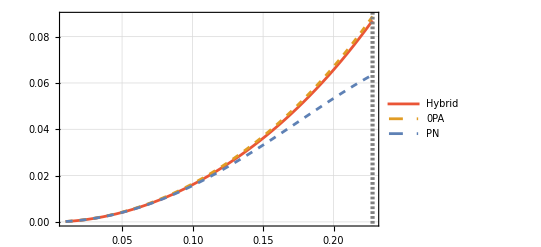

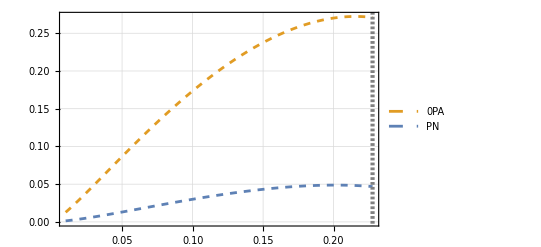

```mathematica
l=3;m=2;a=0.5;ν=0.01;
Clear[hlmSF,phiSF,hlmSFPN,phiSFPN,hlmSFPN,phiSFPN,x]
(*
{hlmSF,phiSF}=hybSF[l,m,x,a];
{hlmPN,phiPN}=hybPN[l,m,x,a,ν];
{hlmSFPN,phiSFPN}=hybPNSF[l,m,x,a];
hlmHyb=hlmSF+N[hlmPN]-N[hlmSFPN];
phiHyb=phiSF+N[phiPN]-N[phiSFPN];
*)

blue=ColorData[97][1];  (*RGBColor[0.368417,0.506779,0.709798]—PN*)
orange=ColorData[97][2];  (*RGBColor[0.880722,0.611041,0.142051]—0PA*)
red=RGBColor[234/255,85/255,54/255]; (*RGBColor[0.922526,0.385626,0.209179]—Hybrid*)

Plot[{
HybridInfAmplPhase[l,m,y,a,ν][[1]],
hybSF[l,m,y,a][[1]],
hybPN[l,m,y,a,ν][[1]]
},
{y,1/100,xISCO[a]},
GridLines -> Automatic, 
Frame -> True, 
(*PlotRange -> {{0.08, 0.17}, {0.9, 1.2}},*)
PlotStyle->{red,{orange,Dashed},{blue,Dashed}},
PlotLegends->{"Hybrid","0PA","PN"},
Epilog->{{
GrayLevel[0.5],
AbsoluteThickness[3],
AbsoluteDashing[{2,1.5}],
InfiniteLine[{ xISCO[a],0},{0,1}]
}}
]

Plot[{
hybSF[l,m,y,a][[2]],
hybPN[l,m,y,a,ν][[2]]
},
{y,1/100,xISCO[a]},
GridLines -> Automatic, 
Frame -> True, 
(*PlotRange -> {{0.08, 0.17}, {0.9, 1.2}},*)
PlotStyle->{{orange,Dashed},{blue,Dashed}},
PlotLegends->{"0PA","PN"},
Epilog->{{
GrayLevel[0.5],
AbsoluteThickness[3],
AbsoluteDashing[{2,1.5}],
InfiniteLine[{ xISCO[a],0},{0,1}]
}}
]
```